```mathematica
RegionPlot3D[x>=0&&y>=0&&z>0&&y<=1+2x&&x^2+y^2+z^2<=4,{x,-0.05,2.5},{y,-0.05,2.5},{z,-0.05,2.5},PlotPoints->100,AxesLabel->Automatic]
```

-Graphics3D-

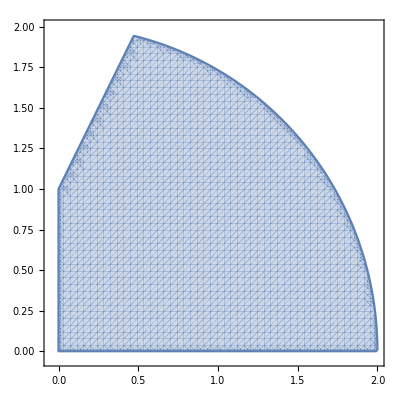

```mathematica
reg=ImplicitRegion[x>=0&&y>=0&&z>0&&y<=1+2x&&x^2+y^2+z^2<=4,{x,y,z}];
RegionPlot[Resolve[Exists[{z},{x,y,z}∈reg],Reals],{x,-.05,2},{y,-.05,2},PlotPoints->50](*xy*)
```

```mathematica
Solve[y==1+2x&&x^2+y^2==4,{x,y}]
```

{{x→1/5 (-2-√19),y→1/5 (1-2 √19)},{x→1/5 (-2+√19),y→1/5+(2 √19)/5}}

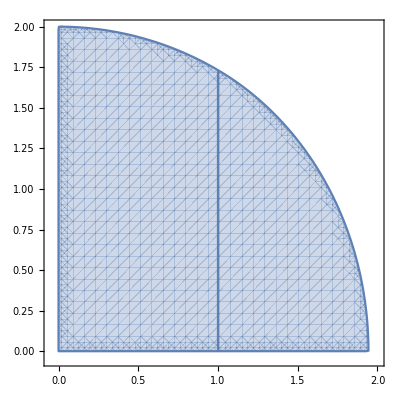

```mathematica
(*yz*)Show[
RegionPlot[Resolve[Exists[{x},{x,y,z}∈reg],Reals],{y,-.05,2},{z,-.05,2},PlotPoints->30],
ContourPlot[y==1,{y,-.05,2},{z,0,√3}]]
```

```mathematica
x^2+y^2+z^2-4/.x->(y-1)/2//Expand
```

-15/4-y/2+(5 y^2)/4+z^2

```mathematica
Solve[-15/4-y/2+(5 y^2)/4+z^2==0,y]
```

{{y→1/5 (1-2 √(19-5 z^2))},{y→2/5 (1/2+√(19-5 z^2))}}

```mathematica
1/2 √(-1+2 y-5 y^2)/.{y->1}
```

ⅈ

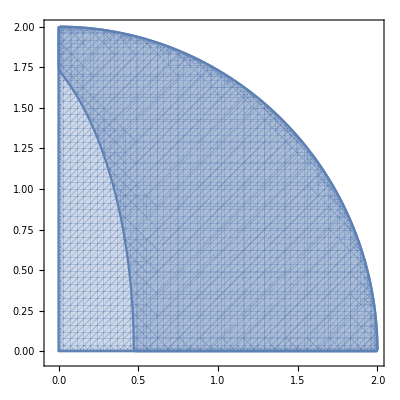

```mathematica
(*xz*)Show[RegionPlot[Resolve[Exists[{y},{x,y,z}∈reg],Reals],{x,-.05,2},{z,-.05,2},PlotPoints->50],RegionPlot[x>=0&&z>=0&&√(4-x^2-z^2)<=1+2x&&x^2+z^2<=4,{x,-.05,2.5},{z,-.05,2.5}]]
```

```mathematica
Reduce[√(4-x^2-z^2)<=1+2x&&x>=0&&z>=0,{x,z}]
```

(0≤x<1/5 (-2+√19)&&√(3-4 x-5 x^2)≤z≤√(4-x^2))||(1/5 (-2+√19)≤x<2&&0≤z≤√(4-x^2))||(x==2&&z==0)